```mathematica
randomNetwork=RandomGraph[BernoulliGraphDistribution[1000,0.002]];
buckets=AssociationThread[VertexList[randomNetwork]->VertexDegree[randomNetwork]];
avalancheSizes={}
```

{}

```mathematica
avalancheSizes={};
Do[seedNode=RandomChoice[VertexList[randomNetwork]];
newBuckets=buckets;
newBuckets[seedNode];
newBuckets[seedNode]+=1;
unstableNodes={seedNode};
While[Length[unstableNodes]>0,currentNode=First[unstableNodes];
unstableNodes=Rest[unstableNodes];
newBuckets[currentNode]-=RandomChoice[{0->1-10^-4,1->10^-4}];
newUnstable=Select[AdjacencyList[randomNetwork,currentNode],newBuckets[#]≥AdjacencyList[randomNetwork,#]&/@AdjacencyList[randomNetwork,currentNode]];
unstableNodes=Join[unstableNodes,newUnstable];AppendTo[avalancheSizes,Length[Select[Values[newBuckets],#≥VertexDegree[randomNetwork,currentNode]&]]]],10000]
avalancheSizes;
```

```mathematica
distributionRandom=Counts[avalancheSizes];
ListLogPlot[SortBy[Normal[distributionRandom],First],PlotLabel->"Avalanche Distribution P(s)",FrameLabel->{"Avalanche Size (s)","Frequency"},Joined->True]
```

-Graphics-

```mathematica
randomNetwork=RandomGraph[BarabasiAlbertGraphDistribution[1000,2]];
buckets=AssociationThread[VertexList[randomNetwork]->VertexDegree[randomNetwork]];
avalancheSizes={}
```

{}

```mathematica
avalancheSizes={};
Do[seedNode=RandomChoice[VertexList[randomNetwork]];
newBuckets=buckets;
newBuckets[seedNode];
newBuckets[seedNode]+=1;
unstableNodes={seedNode};
While[Length[unstableNodes]>0,currentNode=First[unstableNodes];
unstableNodes=Rest[unstableNodes];
newBuckets[currentNode]-=RandomChoice[{0->1-10^-4,1->10^-4}];
newUnstable=Select[AdjacencyList[randomNetwork,currentNode],newBuckets[#]≥AdjacencyList[randomNetwork,#]&/@AdjacencyList[randomNetwork,currentNode]];
unstableNodes=Join[unstableNodes,newUnstable];AppendTo[avalancheSizes,Length[Select[Values[newBuckets],#≥VertexDegree[randomNetwork,currentNode]&]]]],1000]
avalancheSizes;
```

```mathematica
distributionRandom=Counts[avalancheSizes]

ListLogPlot[SortBy[Normal[distributionRandom],First],PlotLabel->"Avalanche Distribution P(s)",FrameLabel->{"Avalanche Size (s)","Frequency"},Joined->True]
```

<|503→175,327→131,999→493,14→2,102→26,54→8,137→28,208→65,17→4,48→13,80→15,37→9,11→2,0→2,13→3,6→1,8→2,63→7,5→2,2→1,20→3,7→1,40→2,28→2,22→1,9→1,24→1|>

-Graphics-

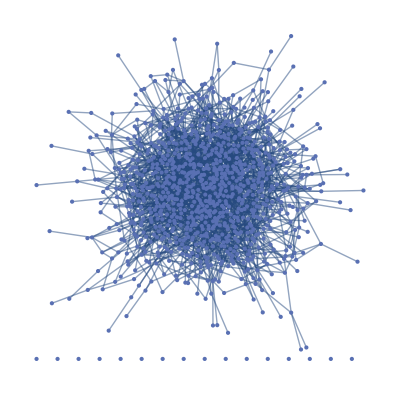

```mathematica
n=1000;
meanDegree=2;
p=(2*meanDegree)/(n-1);
erdosRenyiGraph=RandomGraph[BernoulliGraphDistribution[n,p]]
```

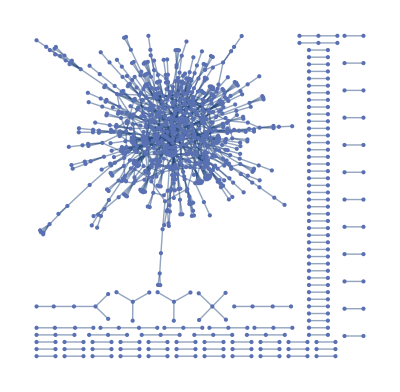

```mathematica
ConfigurationGenerator[N_,gamma_]:=Module[{degreeArray,eachDegreeCount,normalizer,counter,graph},degreeArray={};
eachDegreeCount=Table[i^(-gamma),{i,1,N-1}];
normalizer=N/Total[eachDegreeCount];
eachDegreeCount=Floor[eachDegreeCount*normalizer];
eachDegreeCount[[1]]+=(N-Total[eachDegreeCount]);
Do[counter=eachDegreeCount[[i]];
If[counter≠0,Do[AppendTo[degreeArray,i],{j,1,counter}]],{i,1,N-1}];
graph=RandomGraph[DegreeGraphDistribution[degreeArray]];
Return[graph]]

configurationGraph=ConfigurationGenerator[1000,2];

configurationGraph
```

```mathematica
(*simulate cascade model*)SimulateCascade[graph_,lossProbability_]:=Module[{buckets,unstableNodes,avalancheSize},buckets=ConstantArray[0,VertexCount[graph]];unstableNodes={};Topple[node_]:=(buckets[[node]]-=VertexDegree[graph][[node]];buckets[[AdjacentVertices[graph,node]]]+=1;AppendTo[unstableNodes,AdjacentVertices[graph,node]];AddGrain[]:=(randomNode=RandomInteger[{1,VertexCount[graph]}];
buckets[[randomNode]]+=1;
If[buckets[[randomNode]]>VertexDegree[graph][[randomNode]],Topple[randomNode];];);
(*simulate cascades*)Do[AddGrain[];
While[Length[unstableNodes]>0,unstable=Flatten[unstableNodes];
unstableNodes={};
Do[If[buckets[[node]]>VertexDegree[graph][[node]],Topple[node]],{node,unstable}];];
If[RandomReal[]<lossProbability,Return[0]];(*check for sand loss probability*),10^4];
avalancheSize=Count[buckets,x_/;x>0];(*calculate avalanche size*)Return[avalancheSize];];
configurationGraph=ConfigurationGenerator[1000,2.09];cascadeResultConfiguration=SimulateCascade[configurationGraph,0.0001];
Print[cascadeResultConfiguration];
lambda=2;p=lambda/(n-1);erdosRenyiGraph=RandomGraph[BernoulliGraphDistribution[n,p]];cascadeResultER=SimulateCascade[erdosRenyiGraph,0.0001];Print["Avalanche size for Erdős-Rényi graph: ",cascadeResultER];
```

Part::pkspec1: The expression … cannot be used as a part specification.

Set::pkspec1: The expression … cannot be used as a part specification.

Part::pkspec1: The expression … cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression … cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

Avalanche size for configuration model graph: 521

Part::pkspec1: The expression … cannot be used as a part specification.

Set::pkspec1: The expression … cannot be used as a part specification.

Part::pkspec1: The expression … cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression … cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

Avalanche size for Erdős-Rényi graph: 1000

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

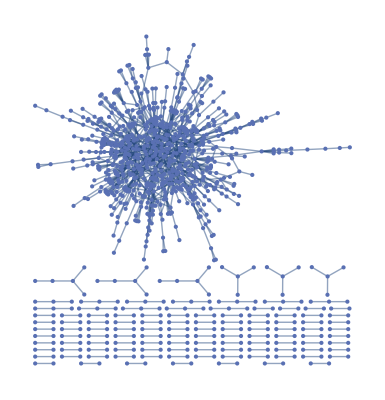

```mathematica
ConfigurationGenerator[n_,gamma_]:=Module[{degreeArray,eachDegreeCount,normalizer,counter,graph},degreeArray={};
eachDegreeCount=Table[i^(-gamma),{i,1,n-1}];
normalizer=n/Total[eachDegreeCount];
eachDegreeCount=Floor[eachDegreeCount*normalizer];
eachDegreeCount[[1]]+=(n-Total[eachDegreeCount]);
Do[counter=eachDegreeCount[[i]];
If[counter≠0,Do[AppendTo[degreeArray,i],{j,1,counter}]],{i,1,n-1}];
graph=RandomGraph[DegreeGraphDistribution[degreeArray]];
Return[graph]]
n=1000;
γ=2;
G1=ConfigurationGenerator[n,γ]
```

```mathematica
SFDegreeArray=VertexDegree[G1];
SFBuckets=AdjacencyList[G1,#]&/@Range[n];
SFSand=ConstantArray[0,n];
sandArray2=ConstantArray[0,n];
```

```mathematica
SimulateSandpile[graph_,bucketSizes_]:=Module[{n=VertexCount[graph],unstableVertices,avalanches,sandArray},
unstableVertices={};
avalanches={};
CheckUnstableVertices[sandArray_]:=Select[Range[n],sandArray[[#]]≥bucketSizes[[#]]&];
PerformTopplings[sandArray_,neighbors_]:=Module[{unstableNodes},unstableNodes=CheckUnstableVertices[sandArray];
Do[sandArray[[i]]=0;
Do[sandArray[[neigh]]++;
If[sandArray[[neigh]]≥bucketSizes[[neigh]],AppendTo[unstableVertices,neigh]];
AppendTo[avalanches,neigh];,{neigh,neighbors[[i]]}];,{i,unstableNodes}];
Return[sandArray]];
(*randomly choose a vertex and add a sand*)randomVertex=RandomInteger[{1,n}];
sandArray[[randomVertex]]++;
If[sandArray[[randomVertex]]≥bucketSizes[[randomVertex]],AppendTo[unstableVertices,randomVertex]];
(*topplings until no unstable vertices left*)While[Length[unstableVertices]>0,sandArray=PerformTopplings[sandArray,AdjacencyList[graph,#]&];
unstableVertices=CheckUnstableVertices[sandArray];];
Return[avalanches]]

degreeSequence=VertexDegree[G1];
buckets2=degreeSequence;avalanches=SimulateSandpile2[G1,buckets2];
Histogram[avalanches,Automatic,"PDF"]
```

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Part::partw: Part 612 of … does not exist.

Do::iterb: Iterator … does not have appropriate bounds.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Part::partw: Part 612 of … does not exist.

Do::iterb: Iterator … does not have appropriate bounds.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Part::partw: Part 612 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Do::iterb: Iterator … does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

$Aborted

-Graphics-

```mathematica
AddGrain[sandArray_,avalanches_]:=Module[{randomNode,unstableList=[]},
randomNode=RandomInteger[{1,Length[sandArray]}];
sandArray[[randomNode]]+=1;

Return[sandArray]]
```

```mathematica
HandleInstability[sandArray_,bucketSizes_,neighbors_]:=Module[{unstableNodes,i},unstableNodes={};
Do[If[sandArray[[i]]≥bucketSizes[[i]],sandArray[[i]]=0;
Do[sandArray[[neigh]]++;
AppendTo[unstableNodes,neigh],{neigh,neighbors[[i]]}]],{i,Length[sandArray]}];
Return[{sandArray,unstableNodes}]]
PerformTopplings[sandArray_,bucketSizes_,neighbors_]:=Module[{unstableNodes,avalancheSize},{sandArray,unstableNodes}=HandleInstability[sandArray,bucketSizes,neighbors];
avalancheSize=Length[unstableNodes];
While[Length[unstableNodes]>0,unstableNodes=DeleteDuplicates[Flatten[neighbors[[unstableNodes]]]];
{sandArray,unstableNodes}=HandleInstability[sandArray,bucketSizes,neighbors];
avalancheSize+=Length[unstableNodes];];
Return[avalancheSize]]
```

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

$Aborted

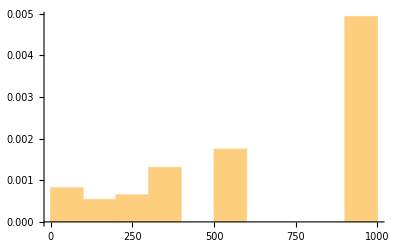

```mathematica
AddGrain[sandArray_]:=Module[{randomNode},randomNode=RandomInteger[{1,Length[sandArray]}];
sandArray[[randomNode]]++;
Return[sandArray]]
HandleInstability[sandArray_,bucketSizes_,neighbors_]:=Module[{unstableNodes,i},unstableNodes={};
Do[If[sandArray[[i]]≥bucketSizes[[i]],sandArray[[i]]=0;
Do[sandArray[[neigh]]++;
AppendTo[unstableNodes,neigh],{neigh,neighbors[[i]]}]],{i,Length[sandArray]}];
Return[{sandArray,unstableNodes}]]
PerformTopplings[sandArray_,bucketSizes_,neighbors_]:=Module[{unstableNodes,avalancheSize},{sandArray,unstableNodes}=HandleInstability[sandArray,bucketSizes,neighbors];
avalancheSize=Length[unstableNodes];
While[Length[unstableNodes]>0,unstableNodes=DeleteDuplicates[Flatten[neighbors[[unstableNodes]]]];
{sandArray,unstableNodes}=HandleInstability[sandArray,bucketSizes,neighbors];
avalancheSize+=Length[unstableNodes];];
Return[avalancheSize]]

SimulateSandpile[n_,bucketSizes_,neighbors_]:=Module[{sandArray,maxTime,avalancheSizes},sandArray=ConstantArray[0,n];
maxTime=10^4;
avalancheSizes={};
Do[sandArray=AddGrain[sandArray];
avalancheSize=PerformTopplings[sandArray,bucketSizes,neighbors];
If[RandomReal[]≤10^(-4),sandArray=RandomChoice[{sandArray,sandArray-1},Length[sandArray]];];
AppendTo[avalancheSizes,avalancheSize];,{i,maxTime}];
Return[avalancheSizes]]

n=1000;
bucketSizes=RandomInteger[{1,10},n];
neighbors=Table[RandomSample[DeleteCases[Range[n],i],RandomInteger[{1,n-1}]],{i,n}];

avalancheSizes=SimulateSandpile[n,bucketSizes,neighbors];
Histogram[avalancheSizes,Automatic,"PDF"]
```

```mathematica
SandTimestep[degreeArray_,sandArray_,neighborsArray_]:=Module[{n=Length[degreeArray],randomNode,failureBool,failureCounter=0},randomNode=RandomInteger[{1,n}];
sandArray[[randomNode]]+=1;
failureBool=If[sandArray[[randomNode]]>degreeArray[[randomNode]],True,False];
sandArray=CascadingFailure[degreeArray,sandArray,neighborsArray,randomNode];
If[RandomReal[]≤10^(-4),sandArray[[RandomInteger[{1,n}]]]-=1;];
Return[{sandArray,failureBool}]]

CascadingFailure[degreeArray_,sandArray_,neighborsArray_,nodeNumber_]:=Module[{n=Length[degreeArray]},If[sandArray[[nodeNumber]]>degreeArray[[nodeNumber]],failureCounter++;
Do[sandArray[[neighbor]]++;,{neighbor,neighborsArray[[nodeNumber]]}];
sandArray[[nodeNumber]]=0;
Do[sandArray=CascadingFailure[degreeArray,sandArray,neighborsArray,neighbor];,{neighbor,neighborsArray[[nodeNumber]]}];];
Return[sandArray]]

n=1000;
gamma=2.09;
SFGraph=ConfigurationGenerator[n,gamma];
SFDegreeArray=VertexDegree[SFGraph];
SFNeighborsArray=AdjacencyList[SFGraph,#]&/@Range[n];
SFSand=ConstantArray[0,n];

maxTime=10^4;
SFFailureSize={};
Do[{SFSand,failureBool}=SandTimestep[SFDegreeArray,SFSand,SFNeighborsArray];
If[failureBool,AppendTo[SFFailureSize,1]];,{i,maxTime}];

Histogram[SFFailureSize,Automatic,"PDF"]
```

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

Set::setps: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»} in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«950»}.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

-Graphics-